# f.figure.series-full.rencon3.strange.baryons-all.band.ci-1.0.nb

******************************** 万年不变的初始化单元

文件绝对路径

```mathematica
filename=NotebookFileName[]
```

C:\octet.formfactor\f.figure.series-full.rencon3.strange.baryons-all.band.ci-1.0.nb

单元对象：第一个单元

```mathematica
cell`title=Cells[]⟦1⟧;
```

刷新第一个单元的名字

```mathematica
NotebookWrite[cell`title,Cell[FileNameSplit[filename]⟦-1⟧,"Title"]]
```

********************************** notebook 备忘录

this nb is to record the all baryon octets ge gm experiment data and calculated data.
extract the Line data, and build the band

增加曲线透明度选项，这样可以隐藏曲线

## parameters

```mathematica
git`root`dir=StringCases[NotebookDirectory[],StartOfString~~((WordCharacter|":"|"\\")..)~~"octet.formfactor"]⟦1⟧
```

C:\octet.formfactor

NumberString 匹配数字字符串

```mathematica
parameter`ci=ToExpression[StringCases[filename,"ci-"~~Pattern[x,NumberString]->x]]⟦1⟧
parameter`ci`string=ToString[NumberForm[parameter`ci,{2,1}]]
```

1.

1.0

```mathematica
parameter`order=StringCases[filename,"series-"~~Pattern[x,Repeated[WordCharacter,4]]->x]⟦1⟧
parameter`order`string=parameter`order
```

full

full

## initial

ge`charge: octet: 1 3 4 6, line, dash, dot, dot-dash

ge`neutral: octet: 2 5 7 8, line, dash, dot, dot-dash

** ** ** ** ** ** ** ** ** ** ** **

gm/μm`charge: octet: 1 3 4 6, line, dash, dot, dot-dash

gm/μm`neutral: octet: 2 5 7 8, line, dash, dot, dot-dash

## import

## import origin figs

{Λ, ci}→

{0.8,1.0} l1c1,{0.9,1.0} l2c1,{1.0,1.0} l3c1,

{0.8,1.5} l1c2,{0.9,1.5} l2c2,{1.0,1.5} l3c2

```mathematica
directory`fig=FileNameJoin[{git`root`dir,"/expression-mfiles/"}]
```

C:\octet.formfactor\expression-mfiles

```mathematica
fig`calc`baryons`ge`total`origin=
(
(Get[
FileNameJoin[{directory`fig,
#1
}
]
])&/@
{
(*+++++++++++++++++++++++++*)
"fig.calc.baryons.ge.tot.L-0.80.ci-1.0.m",
"fig.calc.baryons.ge.tot.L-0.90.ci-1.0.m",
"fig.calc.baryons.ge.tot.L-1.00.ci-1.0.m",

"fig.calc.baryons.ge.tot.L-0.80.ci-1.5.m",
"fig.calc.baryons.ge.tot.L-0.90.ci-1.5.m",
"fig.calc.baryons.ge.tot.L-1.00.ci-1.5.m"
}
);
```

```mathematica
fig`calc`baryons`gm`total`origin=(
(Get[
FileNameJoin[{directory`fig,
#1
}
]
])&/@
{
(*+++++++++++++++++++++++++*)
"fig.calc.baryons.gm.tot.L-0.80.ci-1.0.m",
"fig.calc.baryons.gm.tot.L-0.90.ci-1.0.m",
"fig.calc.baryons.gm.tot.L-1.00.ci-1.0.m",

"fig.calc.baryons.gm.tot.L-0.80.ci-1.5.m",
"fig.calc.baryons.gm.tot.L-0.90.ci-1.5.m",
"fig.calc.baryons.gm.tot.L-1.00.ci-1.5.m"
}
);
```

```mathematica
fig`calc`baryons`ge`total`origin//Dimensions
fig`calc`baryons`gm`total`origin//Dimensions
```

## extract data

```mathematica
{data`f1[x_],data`f1[y_]}^:=data`f2[Join[x,y]]
```

```mathematica
{data`f1[x_]}^:=data`f2[x]
```

将Line中出现的数据用data`f1做tag，并且通过赋上值的方式合并到data`f2

f 是format的意思

```mathematica
fun`data`extract[fig`calc`baryons`ge`total`origin_]:=Table[
Cases[
fig`calc`baryons`ge`total`origin⟦config,io,treeloop⟧
,Line[x_]:>data`f1[x],10(*level*)
]
,{config,1,6,1}
,{io,1,8,1}
,{treeloop,1,3,1}
]
```

```mathematica
data`calc`baryons`ge`total=fun`data`extract[fig`calc`baryons`ge`total`origin];
```

```mathematica
data`calc`baryons`gm`total=fun`data`extract[fig`calc`baryons`gm`total`origin];
```

```mathematica
data`calc`baryons`ge`total//Dimensions
data`calc`baryons`gm`total//Dimensions
```

{6,8,3}

{6,8,3}

## regularize data

```mathematica
{data`rearrange`ge,data`rearrange`gm}=(Transpose[
#1,
{3,1,2}
]&)/@{
data`calc`baryons`ge`total,data`calc`baryons`gm`total
};
```

```mathematica
data`rearrange`ge//Dimensions
data`rearrange`gm//Dimensions
```

{8,3,6}

{8,3,6}

## draw

## initial

指定作图的ci值设定，1;;3,ci==1.0

4;;6,ci==1.5

```mathematica
data`instance=Span[1,3];
```

给定颜色和线型方案，带电粒子4个，中性粒子4个，同样的排列

```mathematica
style`exp={
AbsoluteThickness[_]-> AbsoluteThickness[.8],
PointSize[_]->PointSize[0.02]
};
```

定义用到的颜色方案，带电粒子4个，中性粒子4个，是相同的

mma 默认的图形颜色

```mathematica
color`default = RGBColor[0.368417, 0.506779, 0.709798];
```

1,3,4,6;2,5,7,8

```mathematica
style`colors`theme={Blue,Green,Red,Black};
```

```mathematica
style`colors = {
(*1*)style`colors`theme⟦1⟧,
(*2*)style`colors`theme⟦1⟧,
(*3*)style`colors`theme⟦2⟧,
(*4*)style`colors`theme⟦3⟧,
(*5*)style`colors`theme⟦2⟧,
(*6*)style`colors`theme⟦4⟧,
(*7*)style`colors`theme⟦3⟧,
(*8*)style`colors`theme⟦4⟧
};
```

边框文字的大小

```mathematica
fontsize`frame`text=18;
```

图像的大小

```mathematica
imagesize=Scaled[.6];
```

边框刻度线的粗细

```mathematica
fontsize`frame`tick=AbsoluteThickness[1.5];
```

图例的缩放比例

```mathematica
fig`legend`magni=1;
```

```mathematica
legend`markersize={{50,15}};
```

```mathematica
legend`text`size=16;
```

默认的曲线间填充透明度

```mathematica
style`opacity=Opacity[0];
```

默认线宽

```mathematica
style`line`thick=AbsoluteThickness[2];
```

线型,Dashing[{}]指定线为实线

```mathematica
style`line`type={Dashing[{}],Dashing[Medium],Dashing[{0.001, 0.014}],DotDashed};
```

线型和颜色组合

style`line`type={Dashing[{}],Dashing[Medium],Dotted,DotDashed};

style`colors`theme={Blue,Green,Red,Black};

```mathematica
fun`style`line[a_,b_,c_]:=Directive[style`line`thick,style`line`type⟦a⟧,style`colors`theme⟦b⟧,Opacity[c]]
```

设定八重态曲线style

```mathematica
style`line=Range[8];
style`line⟦{1,3,4,6}⟧={
(*1*){fun`style`line[1,1,0],fun`style`line[3,1,1],fun`style`line[1,1,0]},
(*3*){fun`style`line[2,2,0],fun`style`line[2,2,1],fun`style`line[2,2,0]},
(*4*){fun`style`line[3,3,0],fun`style`line[1,3,1],fun`style`line[3,3,0]},
(*6*){fun`style`line[4,4,0],fun`style`line[4,4,1],fun`style`line[4,4,0]}
};

style`line⟦{2,5,7,8}⟧={
(*2*){fun`style`line[1,1,0],fun`style`line[2,2,1],fun`style`line[1,1,0]},
(*5*){fun`style`line[2,2,0],fun`style`line[1,3,1],fun`style`line[2,2,0]},
(*7*){fun`style`line[3,3,0],fun`style`line[4,4,1],fun`style`line[3,3,0]},
(*8*){fun`style`line[4,4,0],fun`style`line[3,1,1],fun`style`line[4,4,0]}
};
```

*****************************************************  legend

设置图例样式

按照 pr, Σp, Σm, Ξm, {4,3,1,6}

按照 ne, Σ0, Λ, Ξ0, {5,2,8,7}

```mathematica
style`legend1=style`line⟦{4,3,1,6},2⟧;
```

```mathematica
style`legend2=style`line⟦{5,2,8,7},2⟧;
```

设置填充颜色和透明度

```mathematica
style`filling=Table[
{
1->{{2},Directive[style`opacity,style`colors⟦io⟧]},
3->{{2},Directive[style`opacity,style`colors⟦io⟧]}
}
,{io,1,8,1}
];
```

设置框架样式

```mathematica
style`frame={
{
Directive[fontsize`frame`tick,FontSize->fontsize`frame`text,Black],
Directive[fontsize`frame`tick,FontSize->fontsize`frame`text,Black]
},
{
Directive[fontsize`frame`tick,FontSize->fontsize`frame`text,Black],
Directive[fontsize`frame`tick,FontSize->fontsize`frame`text,Black]
}
};
```

## functions to draw

fig`rearrange`ge,fig`rearrange`gm:

{io,treeloop,Λ`ci},{8,3,6}

Λ`ci:{0.80,1.0},{0.90,1.0},{1.00,1.0}

{0.80,1.5},{0.90,1.5},{1.00,1.5}

**********************************

此函数产生带状图

```mathematica
(*io=8;*)treeloop=3;
fig`baryons`band[
data`rearrange_(*the fig data extracted*)
]:=Table[
ListLinePlot[
data`rearrange⟦io,treeloop,data`instance⟧/.{data`f2->Sequence},
PlotStyle->style`line⟦io⟧,
Filling->style`filling⟦io⟧,
PlotRange->Full
]
,{io,1,8,1}
];
```

***************************************

对octet FF 曲线中的点的后续处理

{AbsoluteThickness[_]→AbsoluteThickness[2.5]}
{PointSize[_]→PointSize[0.007],Line→Point},

```mathematica
rule`curve={
{(*PointSize[_]->PointSize[0.007],Line->Point*)},{},{},
{},{},
{},{},
{(*PointSize[_]->PointSize[0.007],Line->Point*)}
};
```

```mathematica
Block[{fig`ge=fig`baryons`band[data`rearrange`ge],fig`gm=fig`baryons`band[data`rearrange`gm]},
baryons`band={
Table[fig`ge⟦io⟧/.rule`curve⟦io⟧,{io,1,8,1}],
Table[fig`gm⟦io⟧/.rule`curve⟦io⟧,{io,1,8,1}]
}
];
```

*****************************************

ge`charge: octet: 1 3 4 6, line, Dashing, Dotted, DotDashed

fig`calc`baryons`ge`total⟦octet,tree-loop-total⟧

横纵轴线标记

```mathematica
framelabel`ge={
{Style["G_E^B(Q^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame`text],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame`text],None}
};
```

```mathematica
framelabel`gm={
{Style["G_M^B(Q^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame`text],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame`text],None}
};
```

对图形的细节进行调整

```mathematica
fun`fig`gegm`cn[
fig`baryons`band_,(*function, generate band figure using data of ge or gm *)
framelabel_,(*framelabel of ge or gm*)
legend`text_,(*legend text*)
legend`ps_:legend`position,(*legend position*)
style`legend_
]:=Legended[
Show[
(Sequence@@fig`baryons`band),
(*Show 接受sequence 序列*) 
ImageSize->Large,
PlotRange->All,
PlotRangePadding->{{0,0},{Scaled[0.09],Scaled[0.09]}},
Frame->True,
FrameLabel->framelabel,
FrameStyle->style`frame

],
(*++++++++++++++++++++++++++++++*)
Placed[
Style[
LineLegend[style`legend,
(Style[#1,FontFamily->"Times New Roman",FontSize->legend`text`size]&)/@legend`text,
(*,LegendFunction->Framed*)
LegendMarkerSize->legend`markersize
],
Magnification->fig`legend`magni
],
legend`ps
]
];
```

## fun apply

### ge`charge

fun`fig`gegm`cn[
baryons`band⟦1,{1,3,4,6}⟧,(*data, generate band figure using data of ge or gm *)
 framelabel_,(*framelabel of ge or gm*)
 legend`text_,(*legend text*)
 legend`ps_: legend`position(*legend position*)
 ]

legend text and legend position

按照 pr, Σp, Σm, Ξm, {4,3,1,6}

按照 ne, Σ0, Λ, Ξ0, {5,2,8,7}

```mathematica
legend`t1={"p","Σ^+","Σ^-","Ξ^-"};
```

```mathematica
legend`ps1={
  {0.78,0.64},(*anchor position*)
  {0.,0.}(*legend anchor*)
};
```

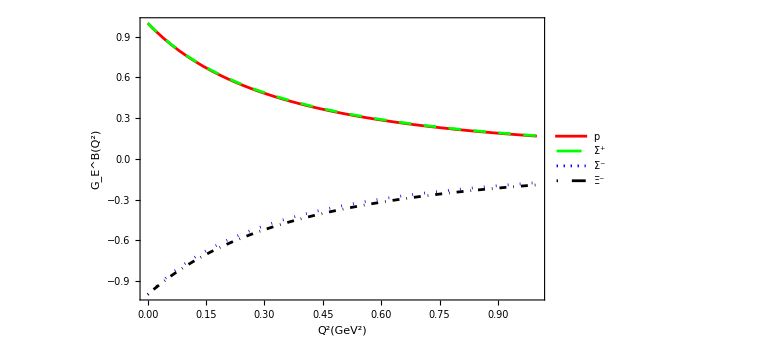

```mathematica
fig`baryons`ge`charge=fun`fig`gegm`cn[
baryons`band⟦1,{4,1,3,6}⟧,
framelabel`ge,
legend`t1,
legend`ps1,
style`legend1
]
```

### ge`neutral

legend text and legend position

按照 ne, Σ0, Λ, Ξ0, {5,2,8,7}

```mathematica
legend`t2={"n","Σ^0","Λ","Ξ^0"};
```

```mathematica
legend`ps2= {
  {0.78,0.64},(*anchor position*)
  {0.,0.}(*legend anchor*)
  };
```

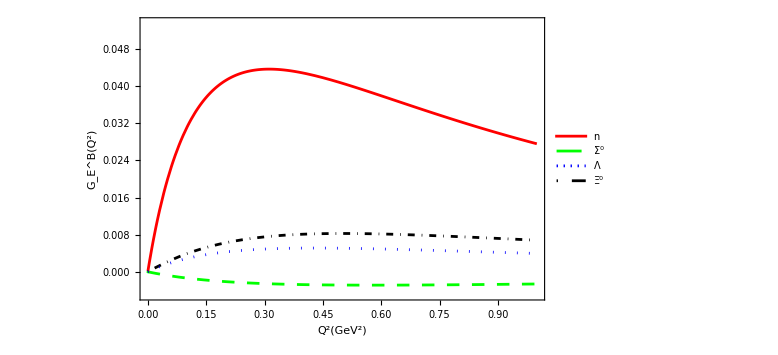

```mathematica
fig`baryons`ge`neutral=fun`fig`gegm`cn[
baryons`band⟦1,{2,5,7,8}⟧,
framelabel`ge,
legend`t2,
legend`ps2,
style`legend2
]
```

### gm`charge

gm`charge: octet: 1 3 4 6, line, Dashing, Dotted, DotDashed

legend`t1={"Σ^-","Σ^+","p","Ξ^-"};

```mathematica
legend`ps3= {
  {0.78,0.64},(*anchor position*)
  {0.,0.}(*legend anchor*)
  };
```

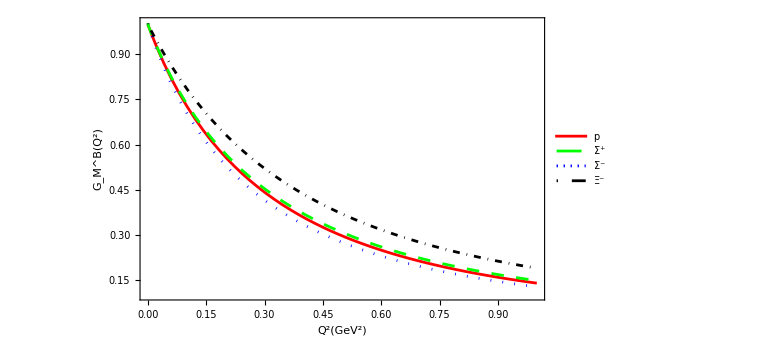

```mathematica
fig`baryons`gm`charge=fun`fig`gegm`cn[
baryons`band⟦2,{4,1,3,6}⟧,
framelabel`gm,
legend`t1,
legend`ps3,
style`legend1
]
```

### gm`neutral

gm`neutral: octet: 2 5 7 8, line, Dashing, Dotted, DotDashed

legend`t2={"Σ^0","n","Ξ^0","Λ"};

```mathematica
legend`ps4= {
  {0.78,0.64},(*anchor position*)
  {0.,0.}(*legend anchor*)
  };
```

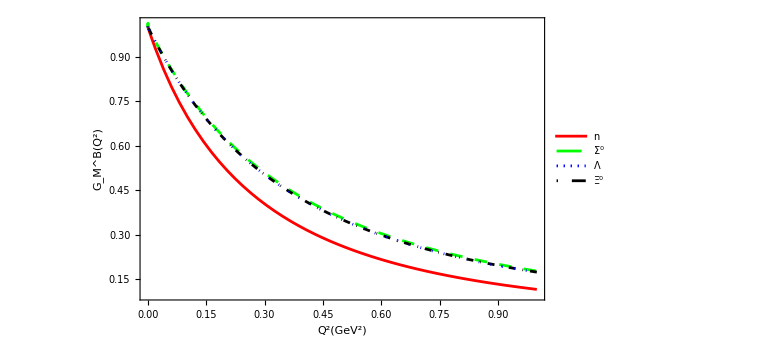

```mathematica
fig`baryons`gm`neutral=fun`fig`gegm`cn[
baryons`band⟦2,{2,5,7,8}⟧,
framelabel`gm,
legend`t2,
legend`ps4,
style`legend2
]
```

## export

```mathematica
output`dir=FileNameJoin[{git`root`dir,"/expression-results/"}]
```

C:\octet.formfactor\expression-results

```mathematica
output`name`list={
FileNameJoin[{output`dir,
"fig`baryons`ge`charge.ed3.ci-"<>
parameter`ci`string<>
".pdf"
}],
FileNameJoin[{output`dir,
"fig`baryons`ge`neutral.ed3.ci-"<>
parameter`ci`string<>
".pdf"
}],
FileNameJoin[{output`dir,
"fig`baryons`gm`charge.ed3.ci-"<>
parameter`ci`string<>
".pdf"
}],
FileNameJoin[{output`dir,
"fig`baryons`gm`neutral.ed3.ci-"<>
parameter`ci`string<>
".pdf"
}]
}
```

{C:\octet.formfactor\expression-results\fig`baryons`ge`charge.ed3.ci-1.0.pdf,C:\octet.formfactor\expression-results\fig`baryons`ge`neutral.ed3.ci-1.0.pdf,C:\octet.formfactor\expression-results\fig`baryons`gm`charge.ed3.ci-1.0.pdf,C:\octet.formfactor\expression-results\fig`baryons`gm`neutral.ed3.ci-1.0.pdf}

```mathematica
output`file`list={fig`baryons`ge`charge,fig`baryons`ge`neutral,fig`baryons`gm`charge,fig`baryons`gm`neutral};
```

```mathematica
Table[
Export[output`name`list⟦i⟧,output`file`list⟦i⟧]
,{i,1,Length[output`file`list],1}];
```